```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["riddle4.tsv"][[All,1]];
```

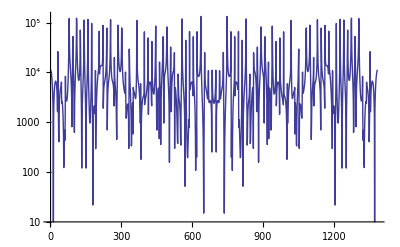

```mathematica
ListLogPlot[Abs[Re[#]]&/@Fourier[data][[2;;]],Joined->True,PlotRange->All]
```

```mathematica
ListPlay@MovingAverage[data,10]
```

-Graphics-

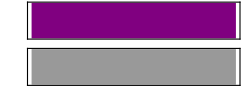

```mathematica
Sound[SoundNote["FSharp2",1]]
```

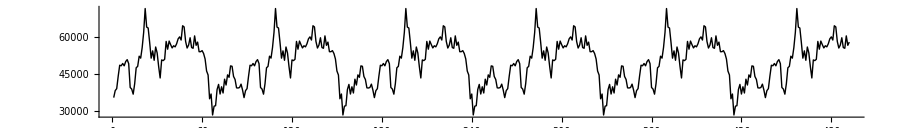

```mathematica
ListPlot[MovingAverage[data[[500;;1000]],10],Joined->True,PlotStyle->Black,AspectRatio->1/7,ImageSize->900]
```

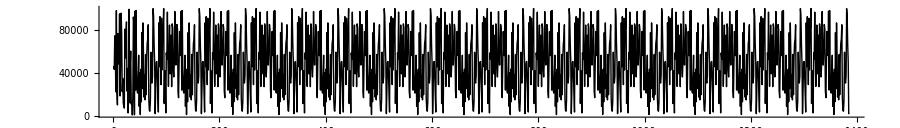

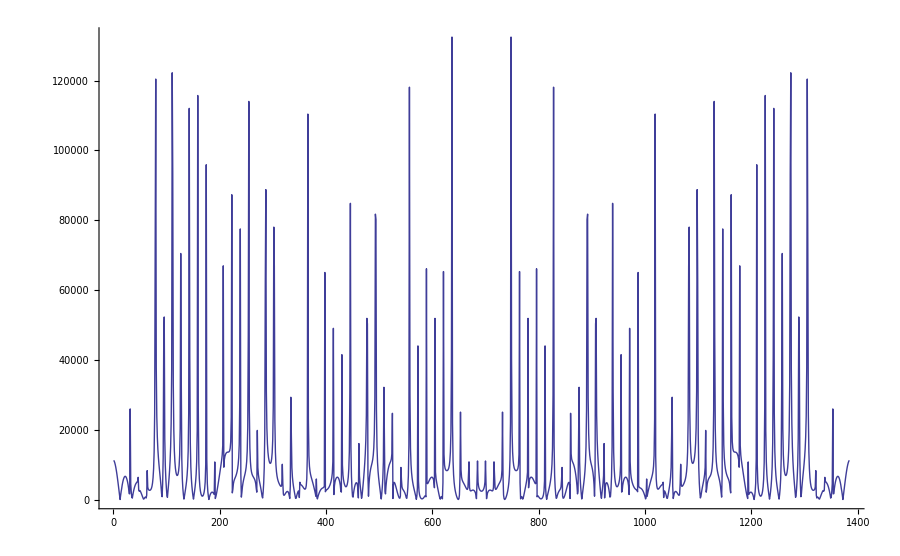

```mathematica
ListPlot[data,Joined->True,PlotStyle->Black,AspectRatio->1/7,ImageSize->900]
ListPlot[Abs[Re[#]]&/@Fourier[data][[2;;]],Joined->True,PlotRange->All]
```

```mathematica
ListPlay[Join[Sequence@@Table[data[[500;;]],{10}]]]
```

-Graphics-

```mathematica
Sound[SoundNote[]]
```

-Graphics-

```mathematica
SawtoothWave[10]
```

0

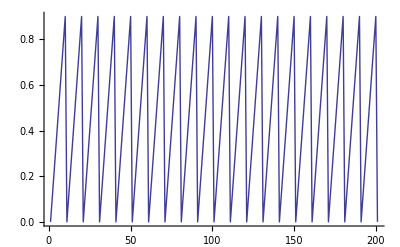

```mathematica
ListPlot[Table[SawtoothWave[x],{x,0,20,.1}],Joined->True]
```

```mathematica
ListPlay[Table[SawtoothWave[x],{x,0,200,.1}]]
```

-Graphics-